```mathematica
SetDirectory[NotebookDirectory[]];
silver=Import["quote-download/XAG.csv", "Table"]//Rest;
decisions=(*Import["filename", "Data"]*)
With[{dates=First/@silver, n=Length@silver}, Transpose[{dates,  RandomReal[{-5,5}, n],RandomReal[{0.25,10}, n]}]];
First/@silver ==First/@decisions
```

True

```mathematica
decisions2=(*Import["filename", "Data"]*)
With[{dates=First/@silver, n=Length@silver}, Transpose[{dates, RandomReal[{-1,1}, n],RandomReal[{0.25,10}, n]}]];
```

```mathematica
invest=1000000;
makeInvestment[{money_,ownedCommodities_}, {leverage_, currPrice_}]:=With[{toSell=ownedCommodities*currPrice},With[{newMoney=money+toSell},
With[{toSpend=newMoney*leverage},
With[{newCommodities=toSpend/currPrice},
{newMoney-toSpend, newCommodities}]]]]
state=FoldList[makeInvestment, {invest,0}, Transpose[{Divide@@@decisions[[All, 2;;3]], Last/@silver}]];
value=First/@state+Last/@state*Last/@Prepend[silver,{0,0}];
```

```mathematica
state2=FoldList[makeInvestment, {invest,0}, Transpose[{Divide@@@decisions2[[All, 2;;3]], Last/@silver}]];
value2=First/@state2+Last/@state2*Last/@Prepend[silver,{0,0}];
```

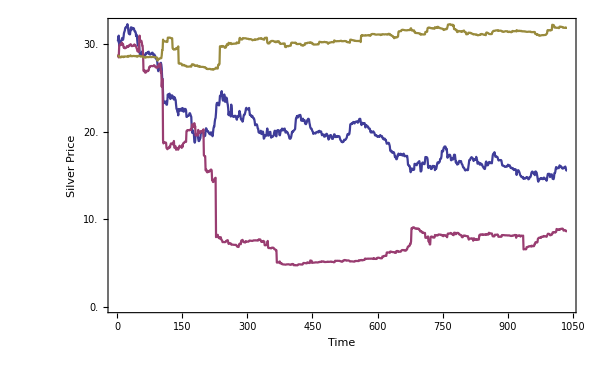
-Graphics-Ag PriceNet ValueTime

```mathematica
Labeled[Labeled[Labeled[TwoAxisListPlot[{{Last@First@silver}~Join~(Last/@silver),{value,value2}},{{Joined->True,ImageSize->600,AxesLabel->{"Time","Silver Price"}}, {PlotStyle->ColorData[1][3],Joined->True,ImageSize->600,AxesLabel->{"Time", "Net Value"}}}],"Ag Price", Left],"Net Value", Right],"Time", Bottom]
```

```mathematica
(* Two axis list plot adopted from docs *)
TwoAxisListPlot[{f_, g_}]:=TwoAxisListPlot[{f, g}, {{},{}}]
TwoAxisListPlot[{f_,g_},{{opts1___}, {opts2___}}, rTickAcc_Integer:4]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks,fstyle, gstyle},
(*Extract plot style*)
fstyle = Sequence@@Cases[{opts1}, (PlotStyle->a_):>a];
gstyle = Sequence@@Cases[{opts2}, (PlotStyle->a_):>a];
fgraph=ListPlot[f,Axes->True,PlotStyle->{ColorData[1][1], fstyle}, opts1];
ggraph=ListPlot[g,Axes->True,PlotStyle->{ColorData[1][2], gstyle}, opts2];
{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];gticks=N@Quiet@Transpose@{fticks,ToString[NumberForm[#,rTickAcc],StandardForm]&/@Rescale[fticks,frange,grange]};Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```